```mathematica
Nt = 551;
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx =551; 
(*xi = -2; xf = 8;*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx;
c =  1;
r = c * (deltat / deltax)//N
```

0.159155

```mathematica
(*xi= 0;
xf = 2*Pi;
h = (2*Pi)/ (Nx);
deltax = h;
deltat = r*h;
deltat / deltax*)


(*(*X = Table[xn = xi + n *deltax, {n, 0, Nx -1}]//N;*)
X=Table[xi+(xf-xi) (i-1)/Nx,{i,1,Nx }]//N;
(*X=(2 π *(X-xi))/(xf-xi);//N*)

(*Xp = Table[xn = xi + n *deltax, {n, 0, Nx }]//N;*)
Xp=Table[xi+(xf-xi) (i-1)/Nx,{i,1,Nx + 1}]//N;
(*Xp=(2 π *(Xp-xi))/(xf-xi);//N*)

T = Table[tn = ti + n *deltat, {n, 0, Nt -1}]//N;*)

T = Table[tn = ti + n *deltat, {n, 0, Nt -1}]//N;
(*For Perodic Interpolation*) 
Xp= Table[xm = xi + m *deltax, {m, 0, Nx}]//N;

X= Table[xm = xi + m *deltax, {m, 0, Nx - 1}]//N;

(*Xp = Table[(i-1)*deltax,{i,1,Nx + 1 }]//N;
X = Table[(i-1)*deltax,{i,1,Nx }]//N;
T = Table[(i-1)*deltat,{i,1,Nt }]//N;*)

f[x_] =ⅇ^(- 8(x-π)^2);
(*f[x_]=f[xi+(((xf-xi)/(2 π))* x)];*)
```

```mathematica
L11 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L11//MatrixForm;
DL11 = -c * L11 * deltat;


L12 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL12 = -c * L12 * deltat;

L22 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL22 = (-c)^2 * L22 * (deltat)^2;

L14 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L14//MatrixForm;
DL14 = -c * L14 * deltat;

L24 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L24//MatrixForm;
DL24 = (-c)^2 * L24 * (deltat)^2;

L34 = (NDSolve`FiniteDifferenceDerivative[Derivative[3],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL34 = (-c)^3 * L34 * (deltat)^3;

L44 = (NDSolve`FiniteDifferenceDerivative[Derivative[4],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL44 = (-c)^4 * L44 * (deltat)^4;
```

```mathematica
(*LD2*)
UCN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UCN[[1,All]] = f[X]//N;
UCN = Chop[N[UCN], 10^(-307)];
UCN = N[UCN];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]


I1 = IdentityMatrix[Length[DL12]];
A = I1 - ((DL12 / 2));
B = I1 + ((DL12 / 2));
MCN = Inverse[A].B;

(*Do[UCN[[n+1,All]] = MCN.UCN[[n,All]], {n,1,Nt - 1 }];*)
Do[UCN[[n+1,All]] = UCN[[n,All]] + (MCN - I1).UCN[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*Euler*)
UEuler= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UEuler[[1,All]] = f[X]//N;
UEuler = Chop[N[UEuler], 10^(-307)];
UEuler = N[UEuler];
UEuler = Developer`ToPackedArray[UEuler, Real]; 
Developer`PackedArrayQ[UEuler]

Ieuler = IdentityMatrix[Length[DL11]];
MEuler = Ieuler +DL11;

Do[UEuler[[n+1,All]] = MEuler.UEuler[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*RK2*)
URK2= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK2[[1,All]] = f[X]//N;
URK2 = Chop[N[URK2], 10^(-307)];
URK2 = N[URK2];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = IdentityMatrix[Length[DL12]];

MRK2 = (IRK2 + (DL12) + ((1/2)*(DL22)));

(*Do[URK2[[n+1,All]] = MRK2.URK2[[n,All]], {n,1,Nt - 1 }];*)
Do[URK2[[n+1,All]] = URK2[[n,All]] + (MRK2 - IRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK4*)
URK4= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK4[[1,All]] = f[X]//N;
URK4 = Chop[N[URK4], 10^(-307)];
URK4 = N[URK4];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = IdentityMatrix[Length[DL14]];

MRK4 = IRK4 + DL14 + ((1/2) * (DL24)) + ((1/6) * (DL34)) + ((1/24) * (DL44));

(*Do[URK4[[n+1,All]] = MRK4.URK4[[n,All]], {n,1,Nt - 1 }];*)
Do[URK4[[n+1,All]] = URK4[[n,All]] + (MRK4 - IRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD4*)

UN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UN[[1,All]] = f[X]//N;
UN = Chop[N[UN], 10^(-307)];
UN = N[UN];
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]


IN = IdentityMatrix[Length[DL14]];
AN = IN - ((DL14 / 2)) + (((DL24)/12));
BN = IN + ((DL14 / 2)) + (((DL24)/12));
MN = Inverse[AN].BN;

(*Do[UN[[n+1,All]] = MN.UN[[n,All]], {n,1,Nt - 1 }];*)
Do[UN[[n+1,All]] = UN[[n,All]] + (MN - IN).UN[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
Dimensions[IN]
```

{551,551}

```mathematica
(************************************************************************************************************************)

(* Eigenvalues*)
```

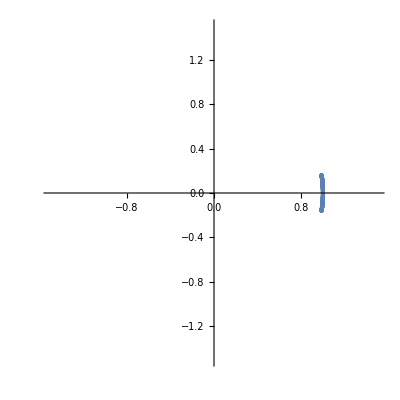

```mathematica
(*CN*)
evals = Eigenvalues[N[MCN]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

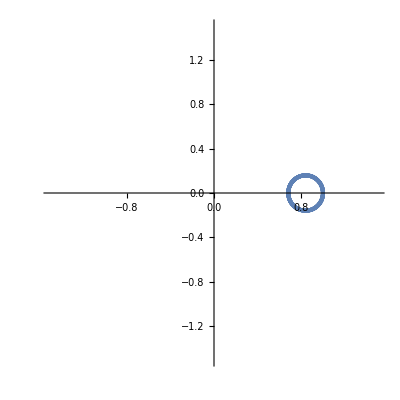

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[MEuler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
ListPlot[Transpose[{realEvalsEuler,imagEvalsEuler}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

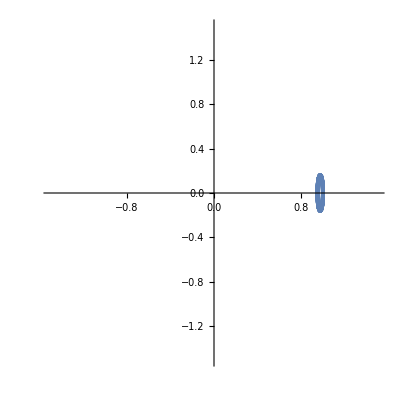

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

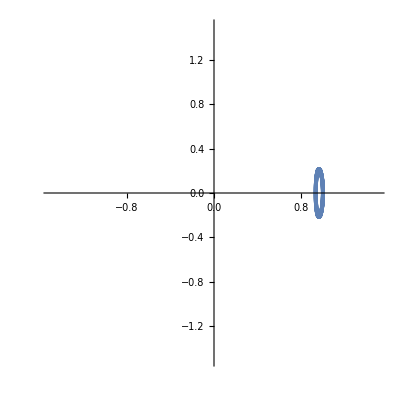

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

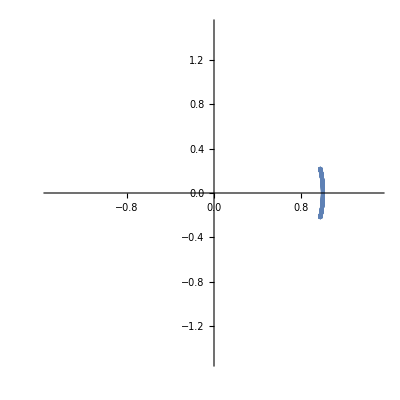

```mathematica
(*LD4*)
evalsN = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
Do[
FCN[[i,All]] = (L12.UCN[[i,All]])^2;

intCN[[i]] = (xf - xi)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intCN}]},Joined->True]*)
```

```mathematica
(*Euler*)
FEuler = Table[0,{i,1,Nt},{j,1,Nx}];
intEuler = Table[0,{i,1,Length[FEuler[[All,1]]]}];
Do[
FEuler[[i]] = (L11.UEuler[[i,All]])^2;

intEuler[[i]] = (xf-xi)/Nx Total[FEuler[[i,All]]]
,{i,1,Length[FEuler[[All,1]]]}];
(*ListPlot[{Transpose[{T,intEuler}]},Joined->True]*)
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
Do[
FRK2[[i]] = (L12.URK2[[i,All]])^2;

intRK2[[i]] = (xf-xi)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
Do[
FRK4[[i]] = (L14.URK4[[i,All]])^2;

intRK4[[i]] = (xf-xi)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},Joined->True]*)
```

```mathematica
(*LD4*)
FN = Table[0,{i,1,Nt},{j,1,Nx}];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
Do[
FN[[i]] = (L14.UN[[i,All]])^2;

intN[[i]] = (xf-xi)/Nx Total[FN[[i,All]]]
,{i,1,Length[FN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intN}]},Joined->True]*)
```

```mathematica
(*actEnergy = ∫_xi^xf (f'[x])^2ⅆx//N*)
```

```mathematica
(*F = f[X];
F' = f'[X];
fexact[t_,x_] = ⅇ^(- 4((x - t)-π)^2);
fderiv[t_,x_] = D[ⅇ^(- 4((x - t)-π)^2),x];
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uderiv = Table[fderiv[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}]//N;
FEnergy = Table[0,{i,1,Nt},{j,1,Nx}];
intEnergy = Table[0,{i,1,Length[FEnergy[[All,1]]]}];
Do[
FEnergy[[i]] = (F')^2;

intEnergy[[i]] = (xf-xi)/Nx Total[FEnergy[[i,All]]];
,{i,1,Length[FEnergy[[All,1]]]}];
ListPlot[{Transpose[{T,intEnergy}]},Joined->True]*)
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD4 = Abs[intN - intN[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
```

```mathematica
(*ListLinePlot[{Transpose[{T,energyErrorLD2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorLD4}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK4}]},Joined->True,PlotRange->All]*)
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(*Error: Evaluate from ti = 0, tf = 2 to ensure that boundry is not reached and Courant number of 0.2 is used*)
```

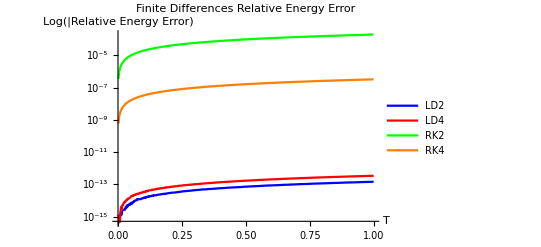

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotStyle->{Blue, Red,Green, Orange},PlotLegends->{"LD2","LD4","RK2","RK4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Finite Differences Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*L1 Error*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = ⅇ^(- 8((x - t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = N[Uexact];
Uexact = Chop[N[Uexact], 10^(-307)];
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
maxabserrLD2 = Max[abserrLD2]
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}]]*)
```

0.00193726

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
maxabserrRK2 = Max[abserrRK2]
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

0.00186367

```mathematica
(*LD4*)
abserrLD4 = Abs[UN-Uexact];
maxabserrLD4 = Max[abserrLD4]
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

3.32257×10^-6

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
maxabserrRK4 = Max[abserrRK4]
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}]]*)
```

3.32405×10^-6

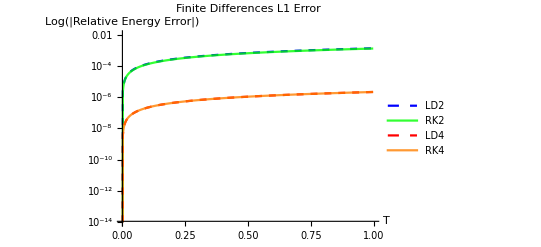

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}]},PlotRange->{{ti,tf},{10^(-14),10^(-2)}}, PlotStyle->{{Blue,Dashed},{Green,Opacity[0.8]},{Red,Dashed},{Orange,Opacity[0.8]}},PlotLabel->"Finite Differences L1 Error",PlotLegends->{"LD2","RK2","LD4","RK4"},AxesLabel->{"T","Log(|Relative Energy Error|)"},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_FD.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
(*Start/Final*)
```

```mathematica
(*LD2*)
LD2start = UCN[[1]];
LD2startErr = UCN[[1]] - Uexact[[1]];
LD2end = Last[UCN];
LD2endErr = Last[UCN] - Last[Uexact];

(*LD4*)
LD4start = UN[[1]];
LD4startErr = UN[[1]] - Uexact[[1]];
LD4end = Last[UN];
LD4endErr = Last[UN] - Last[Uexact];

(*RK2*)
RK2start = URK2[[1]];
RK2startErr = URK2[[1]] - Uexact[[1]];
RK2end = Last[URK2];
RK2endErr = Last[URK2] - Last[Uexact];

(*RK4*)
RK4start = URK4[[1]];
RK4startErr = URK4[[1]] - Uexact[[1]];
RK4end = Last[URK4];
RK4endErr = Last[URK4] - Last[Uexact];

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final.dat",exportData,"Table"];*)
```

```mathematica
aniexact = Animate[Plot[ⅇ^(- 4((x - t)-π)^2),{x,xi,xf},PlotRange->{{xi,xf},{0,1}}],{t,ti,tf}]
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,UCN[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{xi,xf},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,Abs[UCN[[n]] - Uexact[[n]]]}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```